# Prisma

-Graphics-

### Includes

```mathematica
Needs["ErrorBarPlots`"]
```

### Funktionen

```mathematica
Gauss[a_]:={Mean[a],StandardDeviation[a]/(√Length[a])}
```

```mathematica
GError[a_,b_,c_]:= (Total[Map[Abs,MapThread[D,{Table[a,{i,1,Length[b]}],b}]]*c]);
```

```mathematica
FWinkel[w_,dw_]:= Module[{f,fe,a,da},
f=a/2;
fe = GError[f,{a},{da}];
{f,fe}/.{a->w,da->dw}]
```

```mathematica
Fmult[γ_,dγ_,δ_,dδ_]:= Module[{f,fe,a,b,da,db},
f=a*b;
fe = GError[f,{a,b},{da,db}];
{f,fe}/.{a->γ,da->dγ,b-> δ,db->dδ}]
```

## Bestimmen des brechenden Winkels

### Messung

```mathematica
Sa1 ={{4, 6, 7, 3, 9}};
Sa2 ={{0, 1, 2, 3, 4}};
dsa = 0.5;
```

### Rechnung

```mathematica
ϵ = Sa1 - Sa2;
dϵ = 2* dsa;
```

```mathematica
γt = Table[FWinkel[ϵ[[1,x]],dϵ],{x,1,Length[ϵ[[1]]]}] //N
```

(2. | 0.5
2.5 | 0.5
2.5 | 0.5
0. | 0.5
2.5 | 0.5)

```mathematica
γ = Gauss[γt[[1;;Length[γt],1]]]
```

{1.9,0.484768}

## Bestimmen des Brechungsindex n(λ_0)

### Funktionen

```mathematica
Fn[γ_,dγ_,δ_,dδ_]:= Module[{f,fe,a,b,da,db},
f=Sin[(a+b)/2]/Sin[b/2];
fe = GError[f,{a,b},{da,db}];
{f,fe}/.{a->γ,da->dγ,b-> δ,db->dδ}]
```

### Gegeben

```mathematica
λt = {6908,6234,5791,5770,5461,4916,4358,4078,4045}*10^-10;
```

### Messung

```mathematica
SL1 ={{4, 6, 5.5, 5, 6.6}};
SL2 ={{0, 1, 2, 3, 4}};
SK1 ={{7, 8, 10, 8, 12}};
SK2 ={{0, 1, 2, 3, 4}};
Sb1={{5, 6, 7, 8, 9, 10, 11}};
Sb2={{0.5, 1, 2.5, 3, 4.5, 3, 5}};
dsb =dsa; (*ich nehm mal an dassma auf dem gleichen ding messen*)
```

### Rechnung

```mathematica
ωL=SK1-SK2;
ωK=SL1-SL2;
ω=Sb1-Sb2;
dω=2* dsb;
```

```mathematica
δL = Table[FWinkel[ωL[[1,x]],dω],{x,1,Length[ωL[[1]]]}]//N;
```

```mathematica
δK = Table[FWinkel[ωK[[1,x]],dω],{x,1,Length[ωK[[1]]]}]//N;
```

```mathematica
δ= Table[FWinkel[ω[[1,x]],dω],{x,1,Length[ω[[1]]]}]//N;
```

```mathematica
nLt=Table[Fn[γ[[1]],γ[[2]],δL[[x,1]],δL[[x,2]]],{x,1,Length[δL]}];
```

```mathematica
nL = Gauss[nLt[[1;;Length[nLt],1]]];
```

```mathematica
nKt=Table[Fn[γ[[1]],γ[[2]],δK[[x,1]],δK[[x,2]]],{x,1,Length[δK]}];
```

```mathematica
nK = Gauss[nKt[[1;;Length[nKt],1]]];
```

```mathematica
n = Table[Fn[γ[[1]],γ[[2]],δ[[x,1]],δ[[x,2]]],{x,1,Length[δ]}];
```

```mathematica
p1 = Append[Table[{{λt[[x+1]],n[[x,1]]},ErrorBar[0,n[[x,2]]]},{x,1,Length[n]}],{{Last[λt],nK[[1]]},ErrorBar[0,nK[[2]]]}] //N;
p1 = Insert[p1,{{First[λt],nL[[1]]},ErrorBar[0,nL[[2]]]},1]//N
```

({6.908×10^-7,0.427893} | ErrorBar(0.,0.117341)
{6.234×10^-7,0.970399} | ErrorBar(0.,0.379576)
{5.791×10^-7,0.851959} | ErrorBar(0.,0.376117)
{5.77×10^-7,0.970399} | ErrorBar(0.,0.379576)
{5.461×10^-7,0.851959} | ErrorBar(0.,0.376117)
{4.916×10^-7,0.970399} | ErrorBar(0.,0.379576)
{4.358×10^-7,0.434335} | ErrorBar(0.,0.432726)
{4.078×10^-7,0.639366} | ErrorBar(0.,0.391537)
{4.045×10^-7,1.38785} | ErrorBar(0.,0.214436))

```mathematica
pp = Append[Table[{λt[[x+1]],n[[x,1]]},{x,1,Length[n]}],{Last[λt],nK[[1]]}] //N;
pp = Insert[pp,{First[λt],nL[[1]]},1]//N
```

(6.908×10^-7 | 0.427893
6.234×10^-7 | 0.970399
5.791×10^-7 | 0.851959
5.77×10^-7 | 0.970399
5.461×10^-7 | 0.851959
4.916×10^-7 | 0.970399
4.358×10^-7 | 0.434335
4.078×10^-7 | 0.639366
4.045×10^-7 | 1.38785)

```mathematica
pf1=LinearModelFit[pp,x,x]
```

FittedModel[1.21668-724447. x]

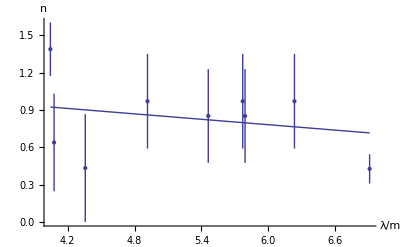

```mathematica
Show[
 ErrorListPlot[p1],
Plot[pf1[x],{x,Min[λt],Max[λt]}],AxesLabel->{"λ/m","n"}]
```

```mathematica
pf1["ParameterTable"]
para1 = pf1["ParameterTableEntries"];
```

| Estimate | Standard Error | t Statistic | P-Value
1 | 1.21668 | 0.591371 | 2.05738 | 0.0786684
x | -724447. | 1.10156×10^6 | -0.657655 | 0.531782

```mathematica
Dis={para1[[2,1]],para1[[2,2]]}
```

{-724447.,1.10156×10^6}

## Auflösungsvermögen

### Messung

```mathematica
t = 4;
dt =0.5;
```

```mathematica
Aufl = Fmult[t,dt,Dis[[1]],Dis[[2]]]
```

{-2.89779×10^6,4.76847×10^6}